## 3.029 Spring 2022 Lecture 01 - 01/31/2022

## Classical Mechanics

Why revisit classical mechanics computationally?

“Undergraduate [physics] students come in expecting that the hardest thing they’ll have to learn will be relativity or quantum mechanics.
Actually those are the most novel topics. The hardest thing that an undergraduate physics student must learn is the classical dynamics of spinning tops”

Fueling your scientific curiosity

Why does dry spaghetti (almost) always break in 3 pieces?

```mathematica
Thumbnail[,300]
```

-Graphics-

How do ‘tears of wine’ form?

```mathematica
Thumbnail[,300]
```

-Graphics-

How does a tippe top invert itself?

```mathematica
Thumbnail[,300]
```

-Graphics-

(one of) 3.029’s class objectives

The hope is, next time you watch a YouTube video about a curious scientific phenomenon, 
or step outside and wonder why ice squeaks underneath your boot, or why icicles form periodic ripples, 
you’ll reach for a notebook (the modern analog for the back of an envelope?) and have fun trying to work it out!

## Pendulum Waves

This is a mesmerizing video demonstration of 15 uncoupled pendula

https://www.youtube.com/watch?v=yVkdfJ9PkRQ

Let’s start by modeling a single pendulum

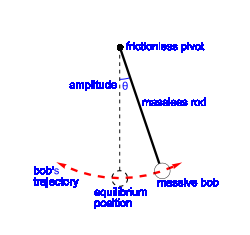

```mathematica
Show[[],ImageSize->250]
```

The equation of motion for a pendulum is given by (we’ll derive this later this week):

### Small-angle Approximation

To solve this analytically, you probably made the “small amplitude” approximation 8.01

For small amplitudes of θ, we may replace sin(θ(t))→θ(t)

```mathematica
DSolveValue[θ''[t] + g/L θ[t]==0,θ[t],t]
```

C[1] Cos[(√g t)/(√L)]+C[2] Sin[(√g t)/(√L)]

This is a 2^nd order ODE

We therefore need 2 initial conditions to specify the two constants above

We’ll set the initial displacement at a symbolic value θ(0)→θ_0

and the initial velocity to zero θ'(0)→0

```mathematica
smallDisplacementSymbolicSolution[θ0_,g_,L_][t_]=DSolveValue[{θ''[t] + g/L θ[t]==0,θ[0]==θ0,θ'[0]==0},θ[t],t]
```

θ0 Cos[(√g t)/(√L)]

Coding comment: We used the pattern function[paramA_,paramB_][argument_] = ...

Will use this pattern frequently, as it achieves two convenient tasks:
	1.  	Separates arguments and parameters, so we can use forms like: 
			function[paramA,paramB]/@listOfArguments
	2.	Provides a convenient way of assigning symbols to expressions, as opposed to something like:
			expressionRHS /.{paramA->.., paramB->..}

The solution is a simple sinusoidal term with a natural frequency ω=√(g/L)

Let’s animate one such pendulum

For g=1,L=1,θ_0=π/12

```mathematica
visualizePendulum[length_,color_:Black][angle_]:=Graphics[{
{color,Line[{{0,0},length {Sin[angle],-Cos[angle]}}]},
{color,PointSize[Large],Point[length {Sin[angle],-Cos[angle]}]}
},PlotRange->1.025{{-1,1},{-1,0}}]
```

```mathematica
With[{g=1,θ0=π/12,L=1},
Animate[visualizePendulum[L][smallDisplacementSymbolicSolution[θ0,g,L][t]],{t,0,60},]
]
```

Coding comment: To keep code concise, we’ll occasionally ‘hide’ unimportant parameters using Iconize.
You can always click on the ‘+‘ sign to Uniconize

It is now straight-forward to add multiple pendula with different lengths

```mathematica
With[{g=1,θ0=π/12},
Animate[Show[
Table[visualizePendulum[length][smallDisplacementSymbolicSolution[θ0,g,length][t]],{length,Subdivide[1/2,1,10]}]
],{t,0,60},]
]
```

This is already very close to the YouTube video!

Note we chose 15 evenly spaced lengths b/w L=[0.5,1]

These all swing at different frequencies and thus take different times to complete one full cycle

We want to choose our lengths in such a way that all the pendula end up at their starting position after 60 seconds

To do this, note that the period of oscillations is related to the natural frequency (and thus the length) using:

If we want the longest pendulum to perform 10 oscillations/cycle
and the shortest pendulum to perform 25 oscillations/cycle
we can write a simple function to compute the desired lengths

```mathematica
simplePendulumLength[g_,{n_,minOscillations_,maxOscillations_}][index_]:=With[{step=(maxOscillations-minOscillations)/n},
g/((2π)^2((minOscillations + step index)/60)^2) ]
```

```mathematica
simplePendulumLength[1,{15,10,25}]/@Range[15]
%//N
```

{900/(121 π^2),25/(4 π^2),900/(169 π^2),225/(49 π^2),4/π^2,225/(64 π^2),900/(289 π^2),25/(9 π^2),900/(361 π^2),9/(4 π^2),100/(49 π^2),225/(121 π^2),900/(529 π^2),25/(16 π^2),36/(25 π^2)}

{0.753629,0.633257,0.53958,0.46525,0.405285,0.356207,0.315533,0.281448,0.252601,0.227973,0.206778,0.188407,0.17238,0.158314,0.145903}

```mathematica
With[{g=1,θ0=π/12,lengths=simplePendulumLength[1,{15,10,25}]/@Range[15]},
Animate[Show[
Table[visualizePendulum[length,RandomColor[]][smallDisplacementSymbolicSolution[θ0,g,length][t]],{length,lengths}]
],{t,0,60},]
]
```

### Large Amplitudes

For larger initial amplitudes, our approximation fails and we must instead solve the equation numerically

We will use ParametricNDSolve to keep the initial amplitude θ_0 as a parameter

```mathematica
parametricNumericSolution=ParametricNDSolveValue[{θ''[t] + g/L Sin[θ[t]]==0,θ[0]==θ0,θ'[0]==0},θ,{t,0,60},{θ0,g,L}]
```

ParametricFunction[<>]

Let’s compare our “true” numerical solution with our analytical approximation

```mathematica
With[{g=1,θ0=π/12,L=1},
Animate[
Show[
{visualizePendulum[L,Black][parametricNumericSolution[θ0,g,L][t]],
visualizePendulum[L,Gray][smallDisplacementSymbolicSolution[θ0,g,L][t]]}
],{t,0,60},]
]
```

And animate our 15 pendula

```mathematica
With[{g=1,θ0=π/4,lengths=simplePendulumLength[1,{15,10,25}]/@Range[15]},
Animate[Show[
Table[visualizePendulum[length,RandomColor[]][parametricNumericSolution[θ0,g,length][t]],{length,lengths}]
],{t,0,60},]
]
```

The lengths we used however, were for the simple pendulum

There’s no-longer a closed-form solution for the pendulum period

We will extract it numerically. To do so, we use a nifty trick by storing the values the pendulum crosses the vertical orientation, 
while swinging counter-clockwise. This is done using the instruction WhenEvent

```mathematica
parametricNumericSolutionPlusPeriod=ParametricNDSolveValue[{θ''[t] + g/L Sin[θ[t]]==0,θ[0]==θ0,θ'[0]==0,WhenEvent[θ[t]==0&&θ'[t]>0,Sow[t]]},θ,{t,0,60},{θ0,g,L},Method->{"ParametricCaching"->None}]
```

ParametricFunction[<>]

Notice that when we evaluate it as normal, it returns the solution as before

```mathematica
parametricNumericSolutionPlusPeriod[π/12,1,1]
```

InterpolatingFunction[…]

If we Reap the Sown results however, we can extract the period by the difference of successive crossings

```mathematica
Reap[parametricNumericSolutionPlusPeriod[π/12,1,1]]
Mean[Differences[First[Last[%]]]]
```

{InterpolatingFunction[…],{{4.73265,11.0429,17.3531,23.6633,29.9735,36.2837,42.5939,48.9041,55.2143}}}

6.31021

Let’s make a function to extract the periods

```mathematica
extractPeriod[θ0_,length_]:=extractPeriod[θ0,length]=Block[{crossings,g=1},
crossings=Reap[parametricNumericSolutionPlusPeriod[θ0,g,length]];
Mean[Differences[First[Last[crossings]]]]]
```

Coding comment: We used the pattern function[paramA_]: = function[paramA] =...

This is called memoization and we will use this occasionally. Essentially, it stores the results of long computations, so we can re-use them!

To extract the pendulum length (i.e. the inverse problem), we’ll interpolate the periods for various values of L and θ_0 (we’ll assume g=1)

```mathematica
periodsInterpolatingFunction=Interpolation[Flatten[Table[{{θ0,length},extractPeriod[θ0,length]},{θ0,Take[Subdivide[0,π/2,12],{2,-2}]},{length,Subdivide[0.1,1.1,12]}],1]];

extractLengths[θ0_]:=Table[
length/.First[FindRoot[60/periodsInterpolatingFunction[θ0,length]==10+i,{length,simplePendulumLength[1.,{15,10,25}][i],0.1,1.1}]],{i,15}]
```

Finally, we can show the full result of our exploration!

```mathematica
With[{g=1,θ0=π/4,lengths=extractLengths[π/4]},
Animate[Show[
Table[visualizePendulum[length,RandomColor[]][parametricNumericSolution[θ0,g,length][t]],{length,lengths}]
],{t,0,60},]
]
```